```mathematica
dir=FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"TestFiles"}]
```

/Users/john/src/chaos/TestFiles

```mathematica
f=First@FileNames[__~~"CH7"~~__~~".cdf",dir]
```

/Users/john/src/chaos/TestFiles/SW_OPER_MAGACH7_2__20220309T000000_20220309T235959_0101.cdf

```mathematica
Needs["NasaCdf`"]
```

```mathematica
readNasaCdf[f,"Variables"]
```

{Timestamp,B_core_nec,B_crust_nec,B_meas_nec}

```mathematica
data=readNasaCdf[f,"Data"];
```

```mathematica
data[[1]]
```

{3.85577×10^9,{2530.19,-575.512,47444.7},{-2.59836,-0.202461,-1.95024},{2483.36,-691.841,47449.1}}

```mathematica
time=data[[All,1]];
```

```mathematica
core=data[[All,2]];
```

```mathematica
crust=data[[All,3]];
```

```mathematica
meas=data[[All,4]];
```

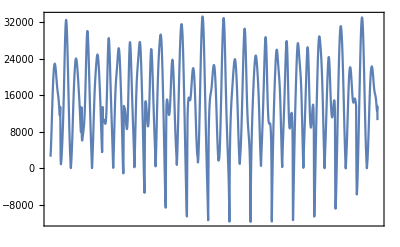

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,core[[All,1]]}],1000]]
```

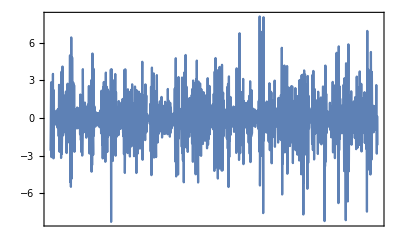

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,1]]}],1000],PlotRange->All]
```

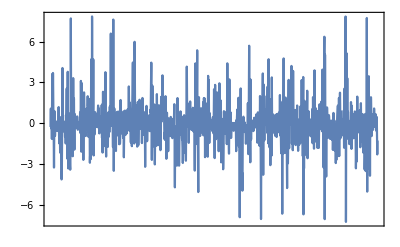

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,2]]}],1000],PlotRange->All]
```

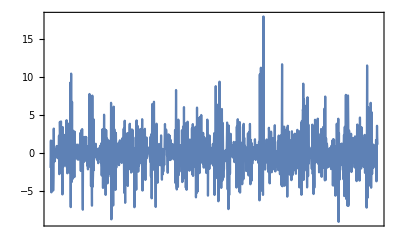

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,crust[[All,3]]}],1000],PlotRange->All]
```

```mathematica
StandardDeviation/@Transpose[core]
```

{9176.77,4932.93,33888.8}

```mathematica
StandardDeviation/@Transpose[crust]
```

{1.64421,1.48458,2.29024}

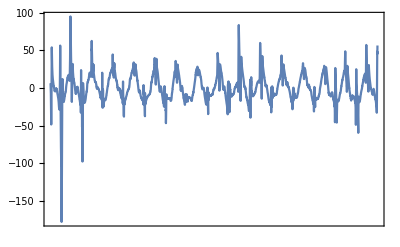

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,meas[[All,3]]-core[[All,3]]-crust[[All,3]]}],1000],PlotRange->All]
```

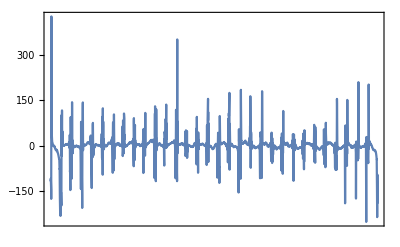

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,meas[[All,2]]-core[[All,2]]-crust[[All,2]]}],1000],PlotRange->All]
```

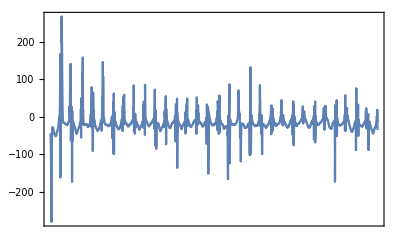

```mathematica
DateListPlot[deleteRedundantPoints[Transpose[{time,meas[[All,1]]-core[[All,1]]-crust[[All,1]]}],1000],PlotRange->All]
```

```mathematica
ind=1;;3000;
```

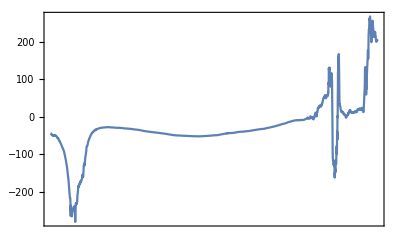

```mathematica
DateListPlot[Transpose[{time[[ind]],meas[[ind,1]]-core[[ind,1]]-crust[[ind,1]]}],PlotRange->All]
```